```mathematica
Numerical example of the quadrature convergence rate for intermediate transition densities
f[x1_,g0_,g1_,g2_,x0_,x2_,n_]:=(1-Exp[-2n(g2-x2)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x2-x1](1-Exp[-2n(g0-x0)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x0-x1]
```

convergence densities example for intermediate Numerical of quadrature rate the transition

Here we define s as the non shifted transition trapezoidal rule and define s2 as the shifted transition trapezoidal rule.

```mathematica
s[h_,g0_,g1_,g2_,x0_,x2_,n_]:=∑_(k=-3 /h)^(g1 /h) f[k h,g0,g1,g2,x0,x2,n]h
s2[h_,g0_,g1_,g2_,x0_,x2_,n_]:=Total[Table[f[k h,g0,g1,g2,x0,x2,n],{k,g1/h,-3/h,-1}]h]
```

Here we define the true integral.

```mathematica
i[g0_,g1_,g2_,x0_,x2_,n_]:=∫_(-∞)^g1 f[x,g0,g1,g2,x0,x2,n]ⅆx
```

Creating a table of values as h goes to 0

```mathematica
a = Table[Abs[s[1/m,1,1.05,1.2,0,0,3]-i[1,1.05,1.2,0,0,3]]//N,{m,1,50}]
```

{0.0302666,0.00114553,0.000417167,0.000187785,0.0000933484,0.0000481513,0.0000244853,0.000011419,4.0195×10^-6,1.64576×10^-7,2.44302×10^-6,3.55594×10^-6,3.94039×10^-6,3.86378×10^-6,3.49436×10^-6,2.94047×10^-6,2.27305×10^-6,1.53921×10^-6,7.70525×10^-7,1.17887×10^-8,5.89759×10^-7,8.56741×10^-7,9.26257×10^-7,8.74943×10^-7,7.54555×10^-7,5.99918×10^-7,4.34267×10^-7,2.72857×10^-7,1.25438×10^-7,2.03835×10^-9,1.06237×10^-7,1.85613×10^-7,2.39832×10^-7,2.69362×10^-7,2.75196×10^-7,2.58643×10^-7,2.21194×10^-7,1.64425×10^-7,8.99256×10^-8,7.37278×10^-10,7.86754×10^-8,1.22748×10^-7,1.41537×10^-7,1.41928×10^-7,1.29434×10^-7,1.08457×10^-7,8.25056×10^-8,5.43568×10^-8,2.61978×10^-8,2.64202×10^-10}

```mathematica
b = Table[Abs[s2[1/m,1,1.05,1.2,0,0,3]-i[1,1.05,1.2,0,0,3]]//N,{m,1,50}]
```

{0.032513,0.000103461,0.0000223078,7.20902×10^-6,2.9787×10^-6,1.44291×10^-6,7.80873×10^-7,4.58488×10^-7,2.8655×10^-7,1.88154×10^-7,1.28586×10^-7,9.08299×10^-8,6.59671×10^-8,4.90575×10^-8,3.72345×10^-8,2.87679×10^-8,2.25764×10^-8,1.79645×10^-8,1.44722×10^-8,1.17887×10^-8,9.69935×10^-9,8.053×10^-9,6.74159×10^-9,5.68658×10^-9,4.83009×10^-9,4.12895×10^-9,3.55054×10^-9,3.06995×10^-9,2.668×10^-9,2.32972×10^-9,2.0434×10^-9,1.79975×10^-9,1.59135×10^-9,1.41226×10^-9,1.25768×10^-9,1.12367×10^-9,1.00705×10^-9,9.05176×10^-10,8.15864×10^-10,7.37278×10^-10,6.67949×10^-10,6.06581×10^-10,5.52102×10^-10,5.03605×10^-10,4.60319×10^-10,4.21585×10^-10,3.86841×10^-10,3.55605×10^-10,3.27459×10^-10,3.02044×10^-10}

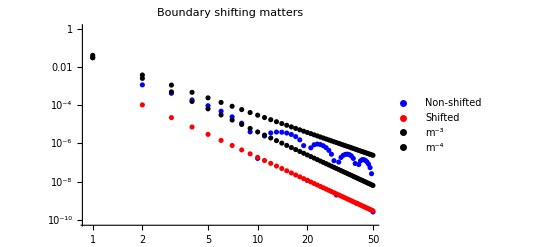

```mathematica
ListLogLogPlot[{a,
b,
Table[0.03/m^3,{m,1,50}],
Table[0.04/m^4,{m,1,50}]},PlotStyle->{Blue,Red,Black,Black},PlotLegends->{"Non-shifted","Shifted","m^-3","m^-4"},PlotLabel->"Boundary shifting matters"]
```

The convergence rate of quadrature with the node shifting gives a h^4 convergence rate. Without shifting, only a subsequence converges at h^4, and the rest of the sequence behaves like h^3.
This suggests that we should center the PSF around the boundary in order to fix the boundary shifting.

```mathematica
c = Table[Abs[s[1/m,1,1.05,1.2,0.8,0.9,3]-i[1,1.05,1.2,0.8,0.9,3]]//N,{m,1,50}]
```

{0.0348684,0.00186898,0.000565431,0.000241667,0.000117371,0.0000597722,0.0000301536,0.0000139868,4.90383×10^-6,2.01562×10^-7,2.96766×10^-6,4.3115×10^-6,4.77078×10^-6,4.67257×10^-6,4.22173×10^-6,3.54963×10^-6,2.74202×10^-6,1.85566×10^-6,9.2843×10^-7,1.42327×10^-8,7.10388×10^-7,1.03198×10^-6,1.1157×10^-6,1.05386×10^-6,9.08805×10^-7,7.2251×10^-7,5.2297×10^-7,3.28564×10^-7,1.51034×10^-7,2.45582×10^-9,1.27895×10^-7,2.23431×10^-7,2.88668×10^-7,3.24182×10^-7,3.31171×10^-7,3.11223×10^-7,2.66136×10^-7,1.97814×10^-7,1.08177×10^-7,8.87326×10^-10,9.46393×10^-8,1.47658×10^-7,1.70264×10^-7,1.70736×10^-7,1.55706×10^-7,1.30472×10^-7,9.92519×10^-8,6.53889×10^-8,3.15143×10^-8,3.17941×10^-10}

```mathematica
d = Table[Abs[s2[1/m,1,1.05,1.2,0.8,0.9,3]-i[1,1.05,1.2,0.8,0.9,3]]//N,{m,1,50}]
```

{0.02954,0.000225332,0.0000329918,9.6775×10^-6,3.83658×10^-6,1.81868×10^-6,9.71725×10^-7,5.65892×10^-7,3.51712×10^-7,2.30027×10^-7,1.56744×10^-7,1.10476×10^-7,8.00976×10^-8,5.94849×10^-8,4.50994×10^-8,3.48132×10^-8,2.73004×10^-8,2.17099×10^-8,1.74803×10^-8,1.42327×10^-8,1.17057×10^-8,9.71552×10^-9,8.13099×10^-9,6.85679×10^-9,5.82273×10^-9,4.9765×10^-9,4.27858×10^-9,3.69885×10^-9,3.21408×10^-9,2.8062×10^-9,2.46103×10^-9,2.16734×10^-9,1.91618×10^-9,1.70038×10^-9,1.51412×10^-9,1.35269×10^-9,1.21221×10^-9,1.0895×10^-9,9.81937×10^-10,8.87326×10^-10,8.03842×10^-10,7.29949×10^-10,6.64356×10^-10,6.05968×10^-10,5.53857×10^-10,5.07229×10^-10,4.65406×10^-10,4.27807×10^-10,3.93929×10^-10,3.6334×10^-10}

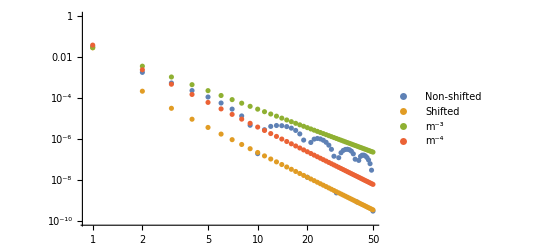

```mathematica
ListLogLogPlot[{c,
d,
Table[0.03/m^3,{m,1,50}],
Table[0.04/m^4,{m,1,50}]},PlotLegends->{"Non-shifted","Shifted","m^-3","m^-4"}]
```

The behaviour appears to be independent of x_0 and x_2